```mathematica
(*1. 定义解析形式的单位脉冲响应 h(n)*)h[n_,r_,theta_]:=Which[theta==0,(n+1) r^n,theta==Pi,(n+1) (-r)^n,True,r^n*Sin[(n+1) theta]/Sin[theta]];

(*2. 参数列表 (5个角度,3个半径)*)
thetas={0,Pi/4,Pi/2,3 Pi/4,Pi};
rs={1/4,1/2,3/4};

(*3. 批量绘图*)
plots=Table[DiscretePlot[h[n,rVal,thetaVal],{n,0,25},PlotRange->{All,{-1.5,2.5}},Filling->Axis,PlotStyle->Directive[Blue,AbsoluteThickness[1]],PlotMarkers->{Automatic,4},AxesLabel->{"n","h(n)"},PlotLabel->Style[Row[{"r=",rVal,", θ=",thetaVal}],11,Bold],ImageSize->250,Ticks->{Automatic,{-1,0,1,2}}],{thetaVal,thetas},{rVal,rs}];

(*4. 显示网格*)
Grid[plots,Frame->All,Spacings->{2,2}]
```

```mathematica
HighResExport[fileName_,plot_]:=Export[fileName,plot,"PNG",ImageResolution->600,Background->White]
```

```mathematica
HighResExport["SecondOrderCompare.png",plots]
```

SecondOrderCompare.png

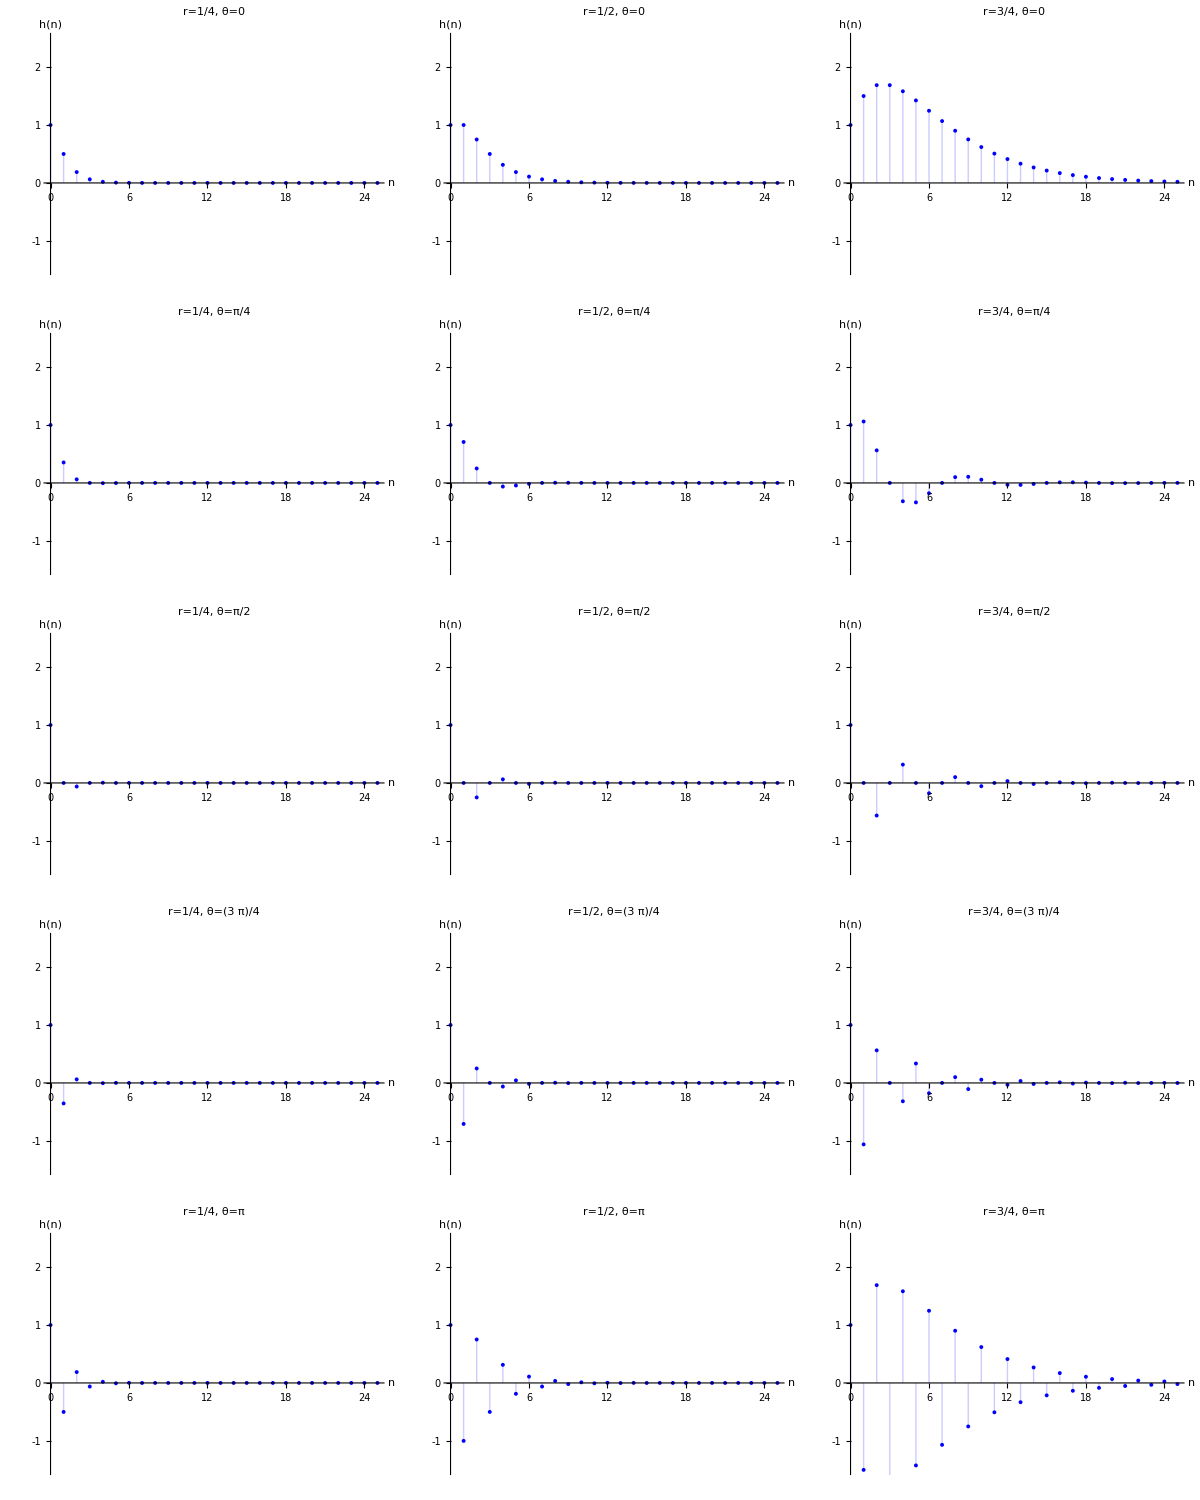

```mathematica
Grid[plots,Frame->All,Spacings->{2,2}]
```